```mathematica
(* 使用二维基元 *)
Disk[]
```

Disk[{0,0}]



```mathematica
Graphics[Disk[]]
```

```mathematica
Graphics[Disk[{0,-3},2]]
```

-Graphics-

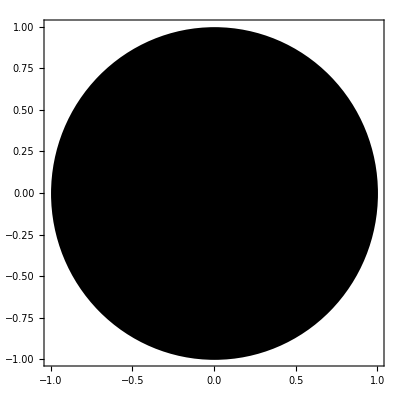

```mathematica
Graphics[Disk[],PlotRange->6,Frame->True]
```

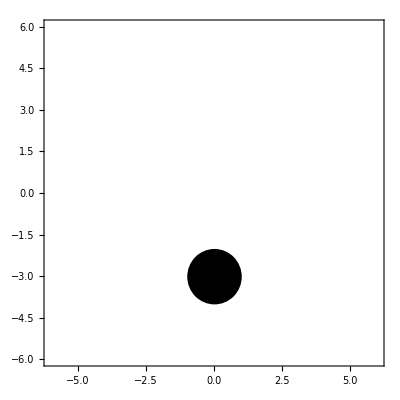

```mathematica
Graphics[Disk[{0,-3}],PlotRange->{{-6,6},{-6,6}},Frame->True]  (* PlotRange如果不加修饰那么默认就为指定数字所示的大小 *)
```



```mathematica
Graphics[Rectangle[{0,0},{3,3}],PlotRange->4,Frame->False]
```

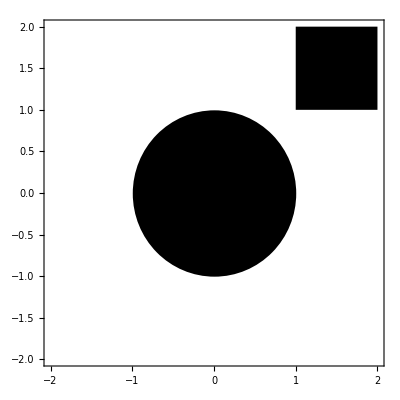

```mathematica
(* 使用多个基元创建图表 *)
Graphics[{Disk[{0,0},1],Rectangle[{1,1},{2,2}]},PlotRange->{{-2,2},{-2,2}},Frame->True]
```

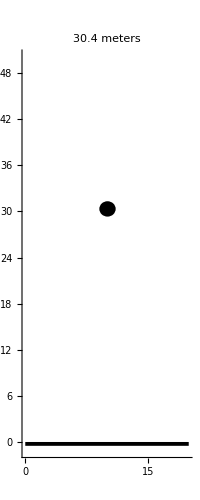

```mathematica
(* 使用图形基元描述自由落体 *)
t =2;
d = 1/2(-9.8)t^2+50;
Graphics[{Disk[{10,d}],Rectangle[{0,-0.5},{20,0}]},PlotRange->{{0,20},{-1,50}},Axes->{False,True},PlotLabel-> ToString[d]<>" meters"]
```

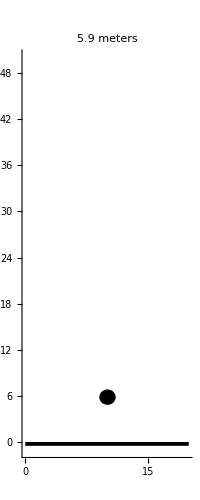

```mathematica
t =3;
d = 1/2(-9.8)t^2+50;
Graphics[{Disk[{10,d}],Rectangle[{0,-0.5},{20,0}]},PlotRange->{{0,20},{-1,50}},Axes->{False,True},PlotLabel-> ToString[d]<>" meters"]
```

```mathematica
DynamicModule[
{d,t},
Manipulate[
	Graphics[{
		Disk[{10,d[t]}],
		Rectangle[{0,-0.5},{20,0}]
	},
	   PlotRange->{{0,20},{-1,50}},
	   PlotLabel->ToString[d[t]]<>"meters"],
	   {t,0,3.2},
	   Initialization :>(d[t_]:=1/2(-9.8)t^2+50)
	]]
```

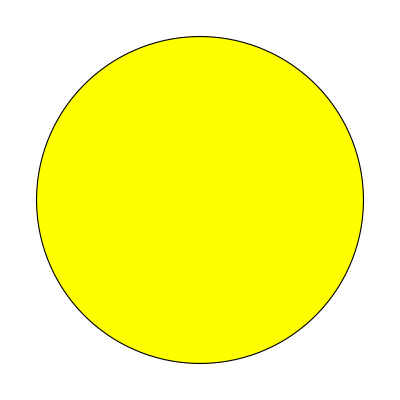

```mathematica
(* 样式化二维图形基元 *)
Graphics[{Yellow,EdgeForm[{Black}],Disk[]}]
```

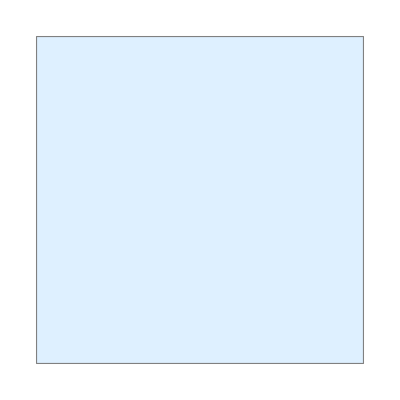

```mathematica
Graphics[{LightBlue,EdgeForm[{Gray,Thick,Dashed}],Rectangle[]}]
```

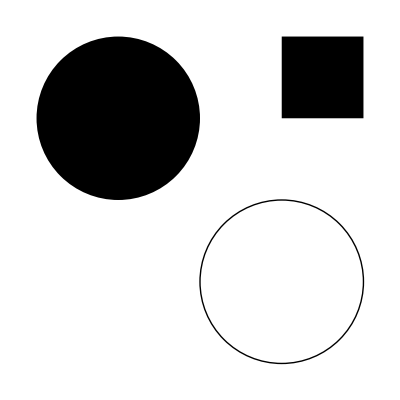

```mathematica
(* 样式的设置会影响其后面基元的显示情况 *)
Graphics[{
	Disk[{-1,1},1],
	Rectangle[{1,1},{2,2}],
	Circle[{1,-1},1]
}]
```

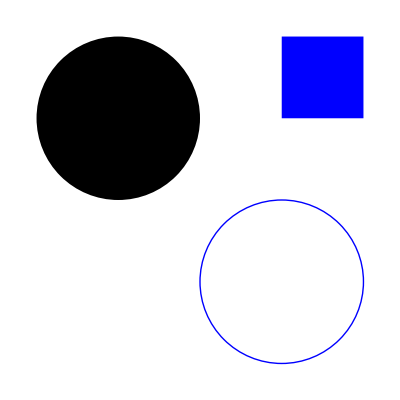

```mathematica
Graphics[{
	Disk[{-1,1},1],
	Blue,Rectangle[{1,1},{2,2}],
	Circle[{1,-1},1]
}]
```

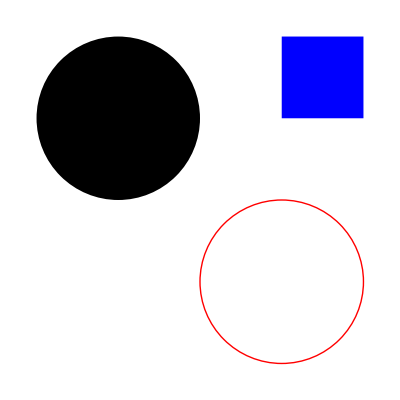

```mathematica
Graphics[{
	Disk[{-1,1},1],
	Blue,Rectangle[{1,1},{2,2}],
	Red, Circle[{1,-1},1]
}]
```

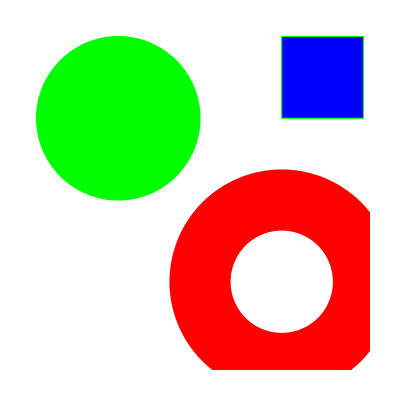

```mathematica
Graphics[
{
	EdgeForm[{Thick,Dashed}],  Green,Disk[{-1,1},1],
							       Blue,Rectangle[{1,1},{2,2}],
							       Red,Thickness[0.11],Circle[{1,-1},1]
}
]
```

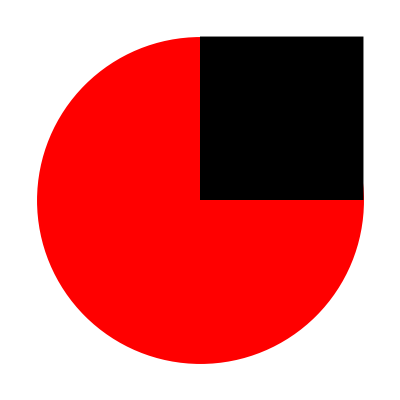

```mathematica
(* 二维基元的重叠渲染 *)
Graphics[
	{Red,Disk[{0,0},1],Black,Rectangle[{0,0},{1,1}]}
]
```

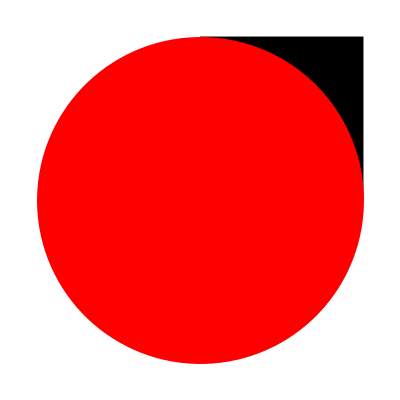

```mathematica
Graphics[
	{Black,Rectangle[{0,0},{1,1}],Red,Disk[{0,0},1]}
]
```

```mathematica
(* 使用三维基元 *)
Graphics3D[Sphere[]]
```

-Graphics3D-

```mathematica
Graphics3D[Sphere[{0,0,0},0.5]]
```

-Graphics3D-

```mathematica
Graphics3D[Sphere[{0,0,0},0.5],PlotRange->{{-1,1},{-1,1},{-1,1}}]
```

-Graphics3D-

```mathematica
(* 样式化三维基元 *)
Graphics3D[{
	Blue,Sphere[{0,0,0},0.5],
	Green,Sphere[{-0.5,-0.5,-0.5},1]
}]
```

-Graphics3D-

```mathematica
(* 设置不透明度 *)
Graphics3D[{
	 Opacity[0.5],
	Blue,Sphere[{0,0,0},0.5],
	Green,Sphere[{-0.5,-0.5,-0.5},1]
}]
```

-Graphics3D-

```mathematica
Graphics3D[{
	 Opacity[0.5],
	Blue,Sphere[{0,0,0},0.5],
	Green,Sphere[{-0.5,-0.5,-0.5},1]
},Boxed->False]
```

-Graphics3D-

```mathematica
Manipulate[
	Graphics3D[{
	 Opacity[0.5],
	Blue,Sphere[{0,0,0},0.5],
	Green,Sphere[{x,y,z},1]
},Boxed->False],
{x,-1,1},{y,-1,1},{z,-1,1}
]
```

```mathematica
DynamicModule[
	{d,t},
	Manipulate[
	Graphics3D[{Sphere[{10,10,d[t]}],Polygon[{{0,0,0},{0,20,0},{20,20,0},{20,0,0}}]},
	PlotRange->{{0,20},{0,20},{0,50}},
	PlotLabel->ToString[d[t]]<>" meters",
	Boxed->False
],
{t,0,3.2},
Initialization:>(d[t_]:=1/2(-9.8)t^2+50)
]]
```

```mathematica
Clear[d,t]
```